## Ricker Standard Figure

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-0.2;
bh=1.2;
```

## Import Data

```mathematica
(* Data directory *)
dataDir="data_export/ricker_trans_rext/";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import[dataDir<>"ews.csv"];
(* Import power spectra DataFrame *)
dfPspec=Import[dataDir<>"pspec.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

5

```mathematica
(* Realisation number to display *)
displayNum=1;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
```

```mathematica
(* Extract info of one trajectory *)
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
tVals = trajVals[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
```

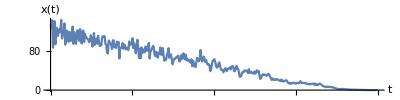

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[trajVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tmax},All}]
```

### Plot format adjustment

```mathematica
dfs
```

```mathematica
rTicks=Round[Range[bh,bl,-0.2],0.1];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

```mathematica
rTicks
```

{1.2,1.,0.8,0.6,0.4,0.2,0.,-0.2}

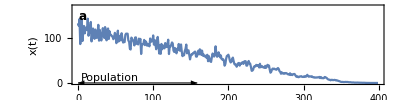

```mathematica
plotTraj=Show[plotX,
PlotRange->{{0,tmax},{0,170}},
ImageSize->imgs,
LabelStyle->ls,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Growth rate, r"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Arrowheads[{-aHeadSize,aHeadSize}*0.7],
Thickness[0.002],
Arrow[{Scaled[{0,0.2},{0,0}],Scaled[{0,0.2},{windowComps*dt2,0}]}]
}
]
```

## EWS Plots

### Variance

```mathematica
(* plot colour *)
colVar=TMBcolours[[2]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
varEws=Table[Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims}];
```

```mathematica
varEws//Dimensions
```

{5,400,2}

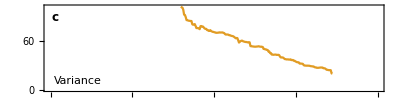

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotVar=ListLinePlot[varEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
(* plot colour *)
colCV=TMBcolours[[3]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
cvEws=Table[Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims}];
```

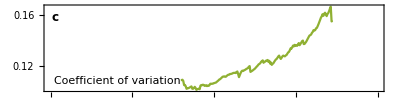

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotVar=ListLinePlot[cvEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colCV,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax/Mean

```mathematica
(* plot colour *)
colSmaxMean=TMBcolours[[4]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Mean"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxMeanEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

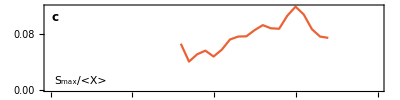

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxMean=ListPlot[smaxMeanEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxMean,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/<X>",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
(* plot colour *)
colSmaxVar=TMBcolours[[5]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxVarEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

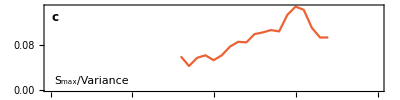

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxMean=ListPlot[smaxVarEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/Variance",ls],textPos,{-1,0}]}]
```

### Autocorrelation (combined)

```mathematica
(* plot colour *)
colAC=TMBcolours[[{4,5,7}]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
```

```mathematica
(* Construct relevant sub dataframe *)
acEws=Table[Cases[dfEws[[2;;,{1,3,indexEws[[i]]}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims},{i,1,3}];
```

```mathematica
acEws//Dimensions
```

{5,3,400,2}

```mathematica
(* line legend *)
legend=LineLegend[colAC,Table["lag-"<>ToString[i],{i,{1,2,3}}],Spacings->{0,0.2},LabelStyle->(ls-1)]
```

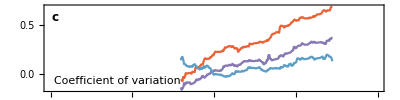

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotAC=ListLinePlot[acEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
PlotRange->{{0,tmax},All},
PlotStyle->colAC,
PlotLegends->Placed[legend,{0.15,0.65}],
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexVar=Position[ewsBootFull[[1,1]],"Variance"][[1,1]];
```

```mathematica
varMeans=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexVar}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
```

```mathematica
(* Compute kendall tau values *)
varKtaus=Table[KendallTau[varMeans[[seed]]][[1,2]],{seed,1,Length[ewsBootFull]}];
```

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[{varKtaus,varKtaus,varKtaus},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colVar,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexSmax=Position[ewsBootFull[[1,1]],"Smax"][[1,1]];
```

```mathematica
smaxMeans=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexSmax}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
```

```mathematica
(* Compute kendall tau values *)
smaxKtaus=Table[KendallTau[smaxMeans[[seed]]][[1,2]],{seed,1,Length[ewsBootFull]}];
```

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[{smaxKtaus,smaxKtaus,smaxKtaus},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colSmax,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{ktauText,
Text[Style["f",labelLetterPosSize,Bold],labelLetterPosBox]}];
```

### Autocorrelation

```mathematica
indexAc1=Position[ewsBootFull[[1,1]],"Lag-1 AC"][[1,1]];
indexAc2=Position[ewsBootFull[[1,1]],"Lag-2 AC"][[1,1]];
indexAc3=Position[ewsBootFull[[1,1]],"Lag-3 AC"][[1,1]];
```

```mathematica
ac1Means=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexAc1}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
ac2Means=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexAc2}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
ac3Means=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexAc3}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
```

```mathematica
(* Compute kendall tau values *)
ac1Ktaus=Table[KendallTau[ac1Means[[seed]]][[1,2]],{seed,1,Length[ewsBootFull]}];
ac2Ktaus=Table[KendallTau[ac2Means[[seed]]][[1,2]],{seed,1,Length[ewsBootFull]}];
ac3Ktaus=Table[KendallTau[ac3Means[[seed]]][[1,2]],{seed,1,Length[ewsBootFull]}];
```

```mathematica
(* Box plot *)
boxAc=BoxWhiskerChart[{ac1Ktaus,ac2Ktaus,ac3Ktaus},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->acCols,
ImageSize->imgsBox,
AspectRatio->aRatio*(imgs/imgsBox),
ImagePadding->padBox,
Epilog->{Text[Style["Kendall τ",ls],Scaled[{0.05,0.25}],{-1,0}],
Text[Style["h",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

```mathematica
ktauTextPos
```

Scaled[{0.05,0.12}]

```mathematica
ktauText
```

Text[Kendall τ,Scaled[{0.05,0.12}],{-1,0}]

### AIC weights - take ensemble of values at time 300

```mathematica
indexWhopf=Position[ewsBootFull[[1,1]],"AIC hopf"][[1,1]];
indexWfold=Position[ewsBootFull[[1,1]],"AIC fold"][[1,1]];
indexWnull=Position[ewsBootFull[[1,1]],"AIC null"][[1,1]];
```

```mathematica
tEval=299;
```

```mathematica
wHopfMeans=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexWhopf}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
wFoldMeans=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexWfold}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
wNullMeans=Table[Cases[ewsBootFull[[seed]][[;;,{1,2,indexWnull}]],{_,"Mean",_}][[;;,{1,3}]],{seed,1,Length[ewsBootFull]}];
```

```mathematica
(* AIC values at time tEval *)
wHopfEvals=Table[FirstCase[wHopfMeans[[seed]],{t_/;t>=tEval,_}],{seed,1,Length[ewsBootFull]}][[;;,2]];
wFoldEvals=Table[FirstCase[wFoldMeans[[seed]],{t_/;t>=tEval,_}],{seed,1,Length[ewsBootFull]}][[;;,2]];
wNullEvals=Table[FirstCase[wNullMeans[[seed]],{t_/;t>=tEval,_}],{seed,1,Length[ewsBootFull]}][[;;,2]];
```

```mathematica
(* Box plot *)
boxAic=BoxWhiskerChart[{wFoldEvals,wHopfEvals,wNullEvals},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{0,1},
ImageSize->imgsBox,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.25]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->aicCols,
ImagePadding->padBox,
Epilog->{
Text[Style["t=300",ls],ktauTextPos,{-1,0}],
Text[Style["j",labelLetterPosSize,Bold],labelLetterPosBox]}
]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Power Spectrum of original series

```mathematica
specData//Dimensions
```

{452,3}

```mathematica
specData[[1]]
```

{Time,Frequency,Empirical}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specData[[2;;,1]]][[1;;;;4]]
```

{199.,279.,359.}

```mathematica
(* Organise list of power spectra *)
pspecs=Table[
Cases[specData,
{i,_,_}]⟦;;,{2,3}⟧,
{i,plotTimes}];
```

```mathematica
(* loop power spectrum for display *)
ωVals=pspecs[[1,;;,1]];
ωValsExt={ωVals-2Pi,ωVals,ωVals+2Pi}//Flatten;
pspecsExt=Table[
Transpose[{ωValsExt,Join[pspecs[[i,;;,2]],pspecs[[i,;;,2]],pspecs[[i,;;,2]]]}],
{i,1,Length[pspecs]}];

(* now trim values *)
len=Dimensions[pspecsExt][[2]];
pspecsExt=pspecsExt[[;;,35;;-35]];
```

```mathematica
pspecs//Dimensions
```

{3,41,2}

```mathematica
timeRange
```

{199.,359.}

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{colFun1[(#-199)/(419-199)]&,timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
timeRange
```

{199.,359.}

```mathematica
Scaled[{textPos[[1,1]],textPos[[1,2]]*0.95}]
```

Scaled[{0.03,0.114}]

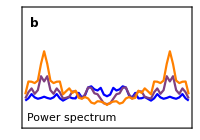

```mathematica
plotPspec=ListLinePlot[pspecsExt,
PlotRange->{-0.01,0.05},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,0.05,0.01]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.55,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAIC,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAic,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotAC,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotSmax,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmax,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotBifTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspec,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

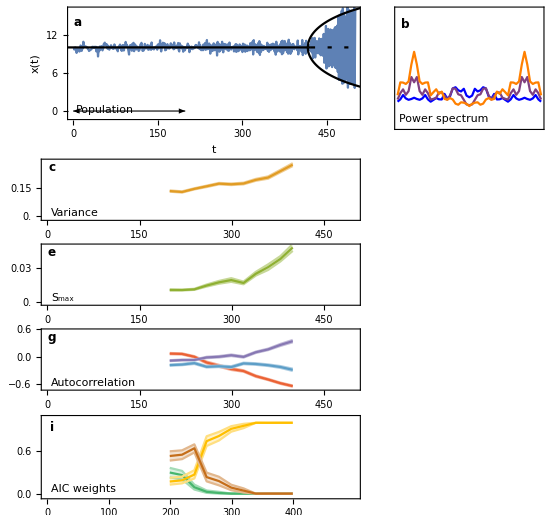

```mathematica
plotGrid
```

```mathematica
Export["figures/fig_ews_flip.png",plotGrid,ImageResolution->400];
```